Converting SYTs & BYWs to Webs — Interactive Notes
Author:  <Noanah Malati>   |   SURF 2025

Definitions
Balanced Yamanouchi Word (BYW) 
An n × k BYW is a word with n letters, each appearing k times, such that in every prefix the number of i’s is ⩾ the number of (i+1)’s.

Standard Young Tableau (SYT)
Rectangle filled with 1…n; rows & columns strictly increase.

```mathematica
Utility code:tidy input& quick checks
```

checks quick (Utility (code:tidy input)&)

```mathematica
(* test if a tableau is standard *)
Clear[isSYT];
isSYT[tab_] := And[
  Flatten[tab] === Range[Total[Length /@ tab]],
  And @@ Flatten@Table[
    OrderedQ[tab[[r]]] && OrderedQ[tab[[All, c]]],
    {r, Length[tab]}, {c, Length[tab[[r]]]}]
];

(* convert a SYT to its BYW / boundary word *)
Clear[tabToBYW];
tabToBYW[tab_] := Module[{rows = Length@tab, word},
  word = ConstantArray[0, Total[Length /@ tab]];
  Do[word[[tab[[r, c]]]] = r, {r, rows}, {c, Length@tab[[r]]}];
  word
];
```

Why?  These helpers let us treat tableaux or BYWs interchangeably.

```mathematica
Drawing webs
```

```mathematica
Clear[webCurvesBezier]
webCurvesBezier[word_List] :=
 Module[{n = Max[word], used = ConstantArray[False, Length@word],
         curves = {}, i, j, h, c1, c2},
  
  Do[
    For[i = 1, i <= Length@word, i++,
      If[word[[i]] == lvl && !used[[i]],
        j = i - 1;
        While[j >= 1 && (used[[j]] || word[[j]] =!= lvl - 1), j--];
        If[j >= 1,
          h  = 1 + 0.5 Abs[i - j];              (* top of the arch        *)
          c1 = {j, h};                          (* control on left  side  *)
          c2 = {i, h};                          (* control on right side  *)
          AppendTo[curves, 
            BezierCurve[{{j, 0}, c1, c2, {i, 0}}]];
          used[[{i, j}]] = True;
        ];
      ];
    ],
    {lvl, n, 2, -1}
  ];
  curves
];

drawWebBezier[word_List] := Graphics[
  {Blue, webCurvesBezier[word],
   Black, Table[Text[word[[k]], {k, 0}], {k, Length@word}]},
  PlotRange -> {{0, Length@word + 1}, {-1, 4}}, ImageSize -> 450
]
```

Rule: pair each n with the nearest unused (n‑1) leftwards; raise arcs so all are visible.

```mathematica
Generating BYWs
```

```mathematica
ClearAll[generateBYWs, randomBYW];

generateBYWs[n_Integer?Positive, k_Integer?Positive] := Module[{words = {}, target = ConstantArray[k, n]},
  ClearAll[extend];
  extend[prefix_, count_] := Module[{next},
    If[Total[count] == n k, AppendTo[words, prefix]; Return[]];
    Do[If[count[[i]] < target[[i]] && (i == 1 || count[[i]] + 1 <= count[[i - 1]]),
        next = ReplacePart[count, i -> count[[i]] + 1];
        extend[Append[prefix, i], next]], {i, n}]];
  extend[{}, ConstantArray[0, n]];
  words];

randomBYW[n_, k_] := RandomChoice[generateBYWs[n, k]];
```

Why recursion?  It enforces the BYW prefix condition on the fly, so we never generate illegal words.

```mathematica
Validation examples
```

{{1,1,2,2,3,3},{1,1,2,3,2,3},{1,2,1,2,3,3},{1,2,1,3,2,3},{1,2,3,1,2,3}}

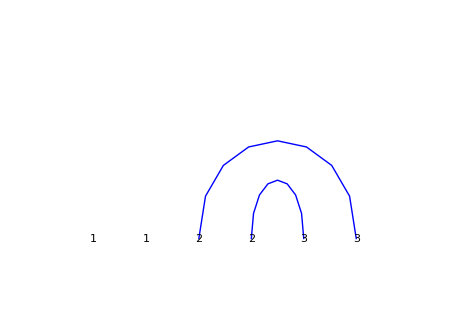
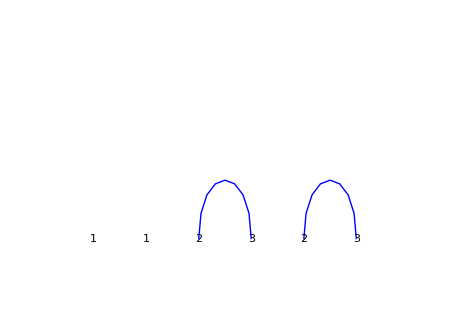
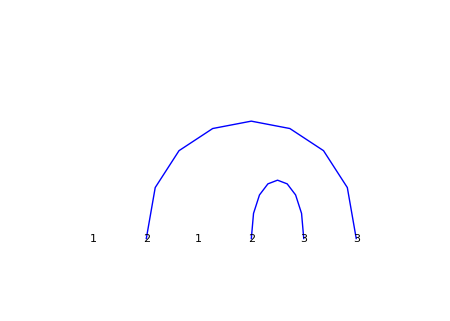
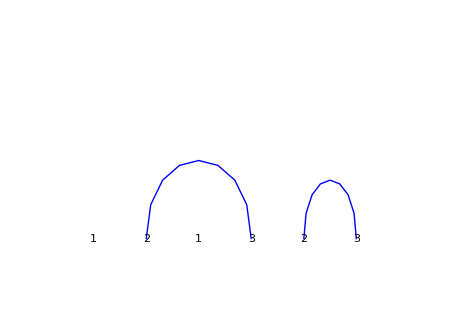
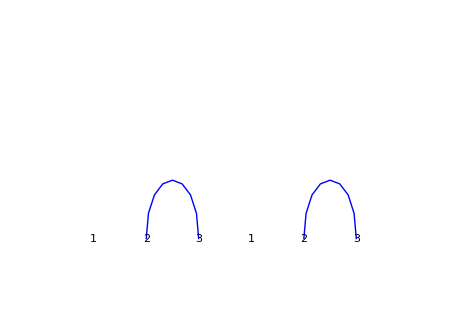

```mathematica
bywList32 = generateBYWs[3, 2];
bywList32
Table[drawWebBezier[word], {word, bywList32}]
```

Should display exactly 5 webs — matches poster count for 3×2.

```mathematica
Interactive sandbox
```

```mathematica
(* ------------  STEP 8  –  WORKING VERSION  ---------------- *)
Manipulate[
 Module[{word = If[mode == "BYW", byw, tabToBYW@syt]},
  Column[{
    Style["Boundary word:  " <> ToString[word], 14, Bold],
    If[VectorQ[word, IntegerQ],
      drawWebBezier[word],
      Style["Invalid BYW list or SYT.", Red]
    ]
  }]
 ],
 
 (* DROPDOWN *)
 {{mode, "BYW", "Input type"}, { "BYW", "SYT" }},
 Delimiter,
 
 (* BYW INPUT FIELD *)
 {{byw, {1,1,2,3,3,2}, "BYW list"},
   ControlType -> InputField, FieldSize -> Medium},
 
 (* SYT INPUT FIELD *)
 {{syt, {{1, 2}, {3, 6}, {4, 5}}, "SYT (rows)"},
   ControlType -> InputField, FieldSize -> Medium},
 
 TrackedSymbols :> {mode, byw, syt}
]
```

Type a tableau (e.g. {{1,4,6},{2,5},{3}}) or BYW list; the graphic updates instantly.

```mathematica
Further exploration
```

•Try  drawWebOffset@randomBYW[4, 2]
•Compare  rotation  of  web  vs . promotion  of  tableau  (future  section)
•Colour  strands  for  sl₄ : label  edges  λ₁, λ₂, …

```mathematica
(* =========================================================== *)
(*  BYW  ->  SYT  AUTO PANEL  +  SMOOTH CURVE  WEB DRAWING      *)
(* =========================================================== *)

(* ----- helper: BYW ➜ SYT (rows of indices) ----------------- *)
Clear[bywToTab]
bywToTab[word_List] := Module[{n = Max[word]},
  Table[Sort @ Flatten @ Position[word, i], {i, 1, n}]
];

(* ----- helper: build smooth upward Bezier arches ------------ *)
Clear[webCurvesSmooth]
webCurvesSmooth[word_List] :=
 Module[{n = Max[word], used = ConstantArray[False, Length[word]],
         curves = {}, i, j, span, h},
  Do[
    For[i = 1, i <= Length[word], i++,
      If[word[[i]] == lvl && ! used[[i]],
        j = i - 1;
        While[j >= 1 && (used[[j]] || word[[j]] =!= lvl - 1), j--];
        If[j >= 1,
          span = i - j;
          h    = 1 + 0.4*span;                        (* arch height *)
          AppendTo[curves,
            BezierCurve[{{j, 0}, {j, h}, {i, h}, {i, 0}}]
          ];
          used[[{i, j}]] = True;
        ];
      ];
    ],
    {lvl, n, 2, -1}
  ];
  curves
];

(* full draw wrapper *)
Clear[drawWebSmooth]
drawWebSmooth[word_List] := Graphics[
  {
    Thick, Blue, webCurvesSmooth[word],
    Black, Table[Text[word[[k]], {k, 0}], {k, Length@word}]
  },
  PlotRange -> {{0, Length@word + 1}, {-1, 1 + 0.4*Length@word}},
  ImageSize -> 450
];

(* ----- interactive panel: one BYW input, auto SYT, smooth web *)
Manipulate[
 Module[{tab = bywToTab[byw]},
  Column[{
    Style["Boundary word (BYW):  " <> ToString[byw], 14, Bold],
    Style["Tableau (rows):       " <> ToString[tab], 14],
    Spacer[5],
    drawWebSmooth[byw]
  }]
 ],
 {{byw, {1, 2, 1, 2, 3, 3}, "BYW list"},
   ControlType -> InputField,
   FieldSize   -> Medium,
   ContinuousAction -> False},          (* updates on Enter *)
 TrackedSymbols :> {byw}
]
```

We’ll add two new abilities:

Rotate the boundary word (geometric move on the web).

Promote the tableau (jeu‑de‑taquin slide).

Then we’ll show the two outputs side‑by‑side to see they match.

Below is a ready‑to‑paste code block. Put it under today’s panel, evaluate, and you’ll get new controls.

```mathematica
(* ====================================================== *)
(*  Rotation  vs.  Promotion  demo                        *)
(* ====================================================== *)

(* ----- 1. rotate the BYW boundary word ---------------- *)
Clear[rotateBoundary]
rotateBoundary[word_List] := RotateLeft[word, 1]     (* pull first item to end *)

(* ----- 2. promotion for a rectangular SYT --------------*)
Clear[promoteSYT]
promoteSYT[tab_List] :=
 Module[{flat = Flatten[tab], n = Length@Flatten[tab], pos, hole},
  
  (* 1. remove NW corner (index 1) -> becomes hole *)
  hole = 1;
  pos  = flat;
  pos[[hole]] = n + 1;               (* mark with big sentinel *)
  
  (* 2. jeu‑de‑taquin slide: bubble the hole SE *)
  While[hole < n - Length[tab] + 1,
    If[hole + Length[tab] <= n && pos[[hole + Length[tab]]] < pos[[hole + 1]],
      pos[[{hole, hole + Length[tab]}]] = pos[[{hole + Length[tab], hole}]];
      hole += Length[tab],
      pos[[{hole, hole + 1}]] = pos[[{hole + 1, hole}]];
      hole += 1
    ]
  ];
  
  (* 3. subtract 1 everywhere; fill hole with n *)
  pos = pos - 1 /. {-1 -> n};
  
  Partition[pos, Length@tab]          (* reshape to tableau rows *)
]

(* ----- 3. Interactive rotation / promotion explorer -----*)
Manipulate[
 Module[{word = byw, rot = rotateBoundary[byw], tab, promo},
  
  tab   = bywToTab[word];
  promo = promoteSYT[tab];
  
  Column[{
    Row[{"Original BYW:  ", word}],
    Row[{"Rotated BYW:   ", rot}],
    Row[{"Original SYT:  ", tab}],
    Row[{"Promoted SYT:  ", promo}],
    Style["Do rotated BYW and promoted SYT match?  " <>
      ToString[rot === tabToBYW@promo], 14, Bold, DarkGreen],
    Spacer[4],
    GraphicsGrid[{
      {drawWebSmooth[word],  drawWebSmooth[rot]},
      {Style["Original web", Bold], Style["Rotated web", Bold]}
    }, Spacings -> {2, 1}]
  }, Spacings -> 1]
 ],
 {{byw, {1, 2, 1, 2, 3, 3}, "BYW list"},
   ControlType -> InputField, FieldSize -> Medium,
   ContinuousAction -> False},
 TrackedSymbols :> {byw}
]
```

```mathematica
2. Drawing a Two-Color Crossing Demo: drawBlueRedCross
```

Purpose : Draw  a  web-like  picture  where
  Blue  arches  connect  every  1 → 2  pair  (using  pairLevel[…]  at  level  2),
  Red  arches  connect  every  2 → 3  pair  (using  pairLevel[…]  at  level  3),
  Each  colour' s  arches  never  cross  themselves, but  blue * red  do  cross .
  Why  this  matters : It  illustrates  the  classical  web  phenomenon  where  same - colour  connections  nest  or  sit  disjoint, yet  different  colours  do  intersect .

```mathematica
drawBlueRedCross[{1, 2, 1, 3, 2, 3}]
```

drawBlueRedCross[{1,2,1,3,2,3}]

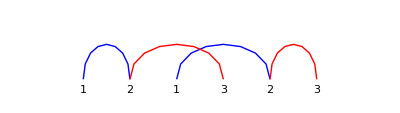

```mathematica
(* ── 1. Helper: pairLevel finds all i->(i-1) pairs for ONE level, independently ── *)
Clear[pairLevel]
pairLevel[word_List, lvl_Integer] := Module[
  {used = ConstantArray[False, Length@word], pairs = {}, i, j},
  For[i = 1, i <= Length@word, i++,
    If[word[[i]] === lvl && ! used[[i]],
      (* find nearest unused (lvl-1) to the left *)
      j = i - 1;
      While[j >= 1 && (used[[j]] || word[[j]] =!= lvl - 1), j--];
      If[j >= 1,
        AppendTo[pairs, {j, i}];
        used[[{i, j}]] = True;  (* mark only for this level *)
      ];
    ];
  ];
  pairs
];

(* ── 2. Draw the crossing demo ── *)
Clear[drawBlueRedCross]
drawBlueRedCross[word_List] := Module[
  {bluePairs, redPairs, h = 1.0},
  
  (* Blue = 2->1, Red = 3->2 *)
  bluePairs = pairLevel[word, 2];
  redPairs  = pairLevel[word, 3];
  
  Graphics[
    {
      (* Blue Bézier arches *)
      Blue, Thick,
      Table[
        With[{l = p[[1]], r = p[[2]]},
          BezierCurve[{{l, 0}, {l, h}, {r, h}, {r, 0}}]
        ],
        {p, bluePairs}
      ],
      
      (* Red Bézier arches *)
      Red, Thick,
      Table[
        With[{l = p[[1]], r = p[[2]]},
          BezierCurve[{{l, 0}, {l, h}, {r, h}, {r, 0}}]
        ],
        {p, redPairs}
      ],
      
      (* Baseline labels *)
      Black,
      Table[Text[word[[k]], {k, -0.2}], {k, Length@word}]
    },
    PlotRange   -> {{0, Length@word + 1}, {-0.5, h + 0.5}},
    ImageSize   -> 400,
    Axes        -> False
  ]
];
drawBlueRedCross[{1, 2, 1, 3, 2, 3}]
```

```mathematica
◉ 3. Interactive Panel
Purpose:Let a user type any BYW into a box and instantly redraw the blue/red crossing demo.Invalid inputs show a friendly warning instead.
```

```mathematica
Manipulate[
  (* guard: only draw if you actually typed a list of integers *)
  If[ListQ[word] && VectorQ[word, IntegerQ],
    drawBlueRedCross[word],
    Style["Please enter a list of integers, e.g. {1,2,1,3,2,3}", 14, Red]
  ],
  
  (* single control: your BYW list *)
  {{word, {1, 2, 1, 3, 2, 3}, "Balanced Yamanouchi Word:"},
   InputField[#, FieldSize -> 25] &},
  
  (* only update on Enter / focus loss *)
  ContinuousAction -> False,
  
  (* nice spacing *)
  ControlPlacement -> Top,
  ContentSize      -> {500, 200}
]
```

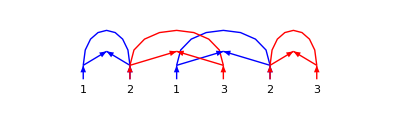

```mathematica
(* ------------------------------------------------------------------ *)
(* 1.   Replace every red×blue crossing in a graphic with a 工 dumbbell *)
Clear[resolveBezierCrossings]
resolveBezierCrossings[g_Graphics, eps_:0.12] := Module[
  {flat, segs, pts, fixes},
  
  (* turn ALL curves into tiny line segments *)
  flat = DiscretizeGraphics[g, MaxCellMeasure -> 0.005];
  segs = Cases[flat, Line[{p_, q_}] :> {p, q}, All];
  
  (* find every pair of segments that cross in the interior *)
  pts = DeleteDuplicates @
    Flatten @ Table[
      With[{pt = Quiet @ RegionIntersection[InfiniteLine[segs[[i]]],
                                            InfiniteLine[segs[[j]]]]},
        If[Head[pt] === Point && pt =!= {}, First @ pt, Sequence[]]],
      {i, Length @ segs}, {j, i + 1, Length @ segs}];
  
  (* build dumbbell at each crossing point *)
  fixes = Flatten @ Table[
    {Black, Thick,
     Line[{p + {-eps, -eps}, p + {-eps, eps}}],
     Line[{p + { eps, -eps}, p + { eps, eps}}],
     Line[{p + {-eps,    0}, p + { eps,    0}}]},
    {p, pts}];
  
  Show[g, Graphics[fixes]]
];

(* ------------------------------------------------------------------ *)
(* 2.   Boundary Y‑split and outward arrows (unchanged)               *)
Clear[splitBoundaryYs, orientEdges]

splitBoundaryYs[g_Graphics] := g /. 
  BezierCurve[{{x_,0},{x_,h_},{y_,h_},{y_,0}}] :>    (* arch endpoints *)
    { Line[{{x,0},{x,0.3}}], Line[{{y,0},{y,0.3}}],
      Line[{{x,0.3}, {(x+y)/2,0.6}}], Line[{{y,0.3}, {(x+y)/2,0.6}}],
      BezierCurve[{{x,0.3},{x,h+0.3},{y,h+0.3},{y,0.3}}]
    };

orientEdges[g_Graphics] := g /. 
  Line[{p1_, p2_}] :> Arrow[Line[{p1, p2}]];

(* ------------------------------------------------------------------ *)
(* 3.   Full pipeline: arches -> dumbbells -> Ys -> arrows               *)
Clear[drawWebGraph]
drawWebGraph[word_List] := Module[{raw},
  raw = drawBlueRedCross[word];       (* use your existing arch function *)
  orientEdges @ splitBoundaryYs @ resolveBezierCrossings[raw]
];
drawWebGraph[{1,2,1,3,2,3}]
```

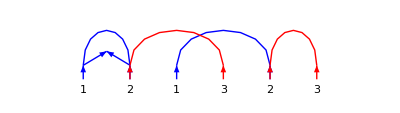

Function::fpct: Too many parameters in {lvl$,pairList$} to be filled from Function[{lvl$,pairList$},Function[{ij$},With[{i$=ij$⟦1⟧,j$=ij$⟦2⟧},{LightGray,Thin,BezierCurve[{{«2»},{«2»},{«2»},{«2»}}]}]]/@pairList$][{1,{{1,2},{4,5},{7,8}}}].

Function::fpct: Too many parameters in {lvl$,pairList$} to be filled from Function[{lvl$,pairList$},Function[{ij$},With[{i$=ij$⟦1⟧,j$=ij$⟦2⟧},{LightGray,Thin,BezierCurve[{{«2»},{«2»},{«2»},{«2»}}]}]]/@pairList$][{2,{{2,3},{5,6},{8,9}}}].

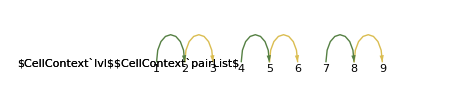

```mathematica
Clear[drawStrandedWebGeneral]
drawStrandedWebGeneral[word_List] := Module[
  {n, pairsByLevel, colors, h = 1.0, delta, skeleton, ribbons, posts, labels},
  
  (* 1) Determine the maximum letter in the word (this is n) *)
  n = Max[word];
  (* That means we have levels λ₁ through λₙ₋₁. *)
  
  (* 2) For each level i=2..n, compute the matching of i-1->i *)
  pairsByLevel = Table[pairLevel[word, lvl], {lvl, 2, n}];
  (* pairsByLevel[[1]] is λ₁ edges, pairsByLevel[[2]] is λ₂, … *)
  
  (* 3) Choose a distinct colour for each level λᵢ *)
  colors = Table[ColorData["DarkRainbow"][i/(n)], {i, 1, n - 1}];
  (* colours[[1]] for λ₁, colours[[2]] for λ₂, etc. *)
  
  (* 4) Draw the gray skeleton arches for *every* pair, all at height h *)
  skeleton = Flatten @ Map[
    Function[{lvl, pairList},
      Map[
        Function[{ij},
          With[{i = ij[[1]], j = ij[[2]]},
            {LightGray, Thin,
             BezierCurve[{{i, 0}, {i, h}, {j, h}, {j, 0}}]}
          ]
        ],
        pairList
      ]
    ],
    Transpose[{Range[n - 1], pairsByLevel}]
  ];
  
  (* 5) Overlay the colored, arrow-headed ribbons level by level *)
  ribbons = Flatten @ MapIndexed[
    Function[{pairList, lvlIdx},
      Module[{c = colors[[lvlIdx]], δ = 0.03, lvl = lvlIdx},
        Map[
          Function[{ij},
            Module[{i = ij[[1]], j = ij[[2]]},
              (* We choose the arrow direction to be from i->j *)
              {c, Thick, Arrowheads[0.04],
               Arrow[BezierCurve[{{i, δ}, {i, h + δ}, {j, h + δ}, {j, δ}}]]}
            ]
          ],
          pairList
        ]
      ]
    ],
    pairsByLevel
  ];
  
  (* 6) Label the baseline posts *)
  posts = Range[Length[word]];
  labels = Map[{Black, Text[ToString[#], {#, -0.15}]} &, posts];
  
  (* 7) Assemble everything *)
  Graphics[
    {
      skeleton,
      ribbons,
      labels
    },
    PlotRange -> {{0, Length[word] + 1}, {-0.5, h + 0.5}},
    ImageSize -> 450,
    Axes -> False
  ]
]
(* For an sl₄ example, say the BYW = {1,2,3,1,2,3,1,2,3} 
   (that’s the 3×3 case but with 3 colours) *)

drawStrandedWebGeneral[{1, 2, 3, 1, 2, 3, 1, 2, 3}]
```